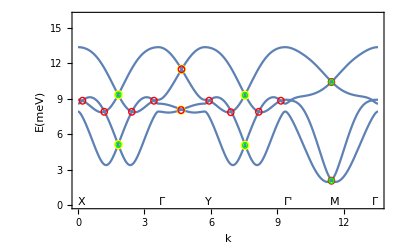

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0.45;
phx=0;
phy=0;
phz=0;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];
reflection={{0.20358469308229177,8.830365851876385},{1.183807315371466,7.89315877357795},{2.427936028276957,7.89315877357795},{3.427009085610154,8.830365851876385},{5.915266511421139,8.830365851876385},{6.8954891337103135,7.857112347489549},{8.158468281659827,7.89315877357795},{9.157541338993026,8.830365851876385},{11.438443979319757,10.416408599766045},{11.438443979319757,2.0536377472569285},{4.6522873634716255,8.037344477931555},{4.671137798515646,11.497801382418086}};
timereversal={{1.8247221068682342,5.108960682088044},{1.8247221068682342,9.335015817114009},{7.5364039252070825,9.298969391025608},{7.5364039252070825,5.045491112594247},{4.6522873634716255,8.037344477931555},{4.671137798515646,11.497801382418086}};
cobination={{1.8247221068682342,5.108960682088044},{1.8247221068682342,9.335015817114009},{7.5364039252070825,9.298969391025608},{7.5364039252070825,5.045491112594247},{11.438443979319757,10.416408599766045},{11.438443979319757,2.0536377472569285}};


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},FrameLabel->{{"E(meV)",None},{"k",None}},FrameTicks->{None,Automatic},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->Join[Table[{Yellow,Circle[timereversal[[i]],{0.17,0.17*2}]},{i,1,6}],Table[{Red,Circle[reflection[[i]],{0.14,0.14*2}]},{i,1,12}],Table[{Green,Circle[cobination[[i]],{0.11,0.11*2}]},{i,1,6}],{Inset["X",{0.15,0.25}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.25}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.25}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.16,0.25}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.15,0.25}],Inset["Γ",{4Pi/Sqrt[3]+2Pi-0.15,0.25}]}],Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

### breaking time reversal symmetry

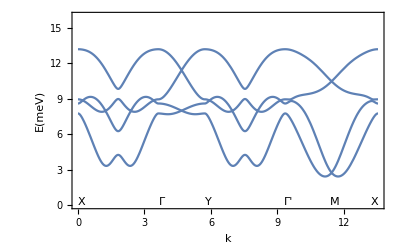

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0.45;
phx=-0.5;
phy=0.5;
phz=0;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},FrameLabel->{{"E(meV)",None},{"k",None}},FrameTicks->{None,Automatic},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.15,0.25}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.25}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.25}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.16,0.25}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.15,0.25}],Inset["Γ",{4Pi/Sqrt[3]+2Pi-0.15,0.25}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

### breaking time reversal and inversion but leave combination

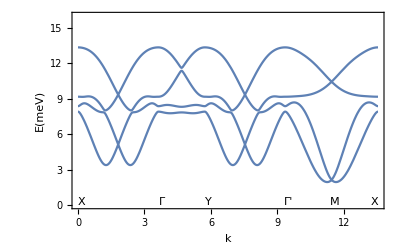

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0.45;
phx=0.5;
phy=0.5;
phz=0.5;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},FrameLabel->{{"E(meV)",None},{"k",None}},FrameTicks->{None,Automatic},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.15,0.25}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.25}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.25}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.16,0.25}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.15,0.25}],Inset["Γ",{4Pi/Sqrt[3]+2Pi-0.15,0.25}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

### Break T ,R, and their combination

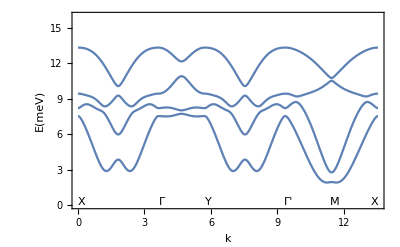

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0.45;
phx=-0.5;
phy=0.5;
phz=1;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},FrameLabel->{{"E(meV)",None},{"k",None}},FrameTicks->{None,Automatic},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.15,0.25}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.25}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.25}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.16,0.25}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.15,0.25}],Inset["Γ",{4Pi/Sqrt[3]+2Pi-0.15,0.25}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

### Critical magnetic field

1. in ac plane H//c’

```mathematica
hv1={0,0,1};
```

2. in ac plane H |_ c’

```mathematica
hv2={1,1,0}/Sqrt[2];
```

3. out ac plane H//c’, assume c’ is along sx direction, which is same with sy

```mathematica
hv3={1,0,0};
```

4. out ac plane H|_c’

```mathematica
hv4={0,1,1}/Sqrt[2];
```

5. Inplane 45 degree from reflection plane.

```mathematica
hv5={0.21132486540518702,-0.7886751345948129,0.5773502691896257};
```

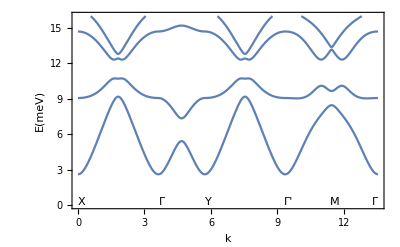

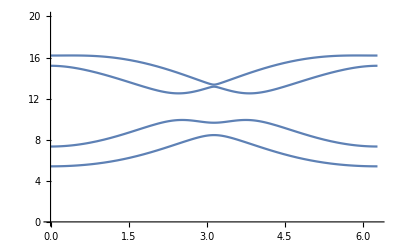

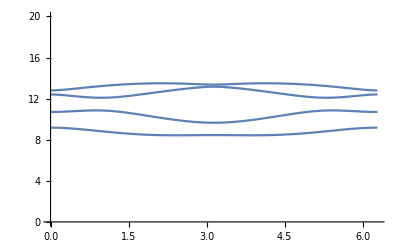

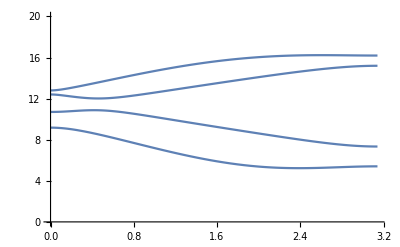

{1.92073,1.58989,1.92073,1.58989,1.8182,1.44553×10^-7,1.8182,1.44548×10^-7}

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=-3.2;
{phx,phy,phz}=1*hv5;

pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},FrameLabel->{{"E(meV)",None},{"k",None}},FrameTicks->{None,Automatic},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.15,0.25}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.25}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.25}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.16,0.25}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.15,0.25}],Inset["Γ",{4Pi/Sqrt[3]+2Pi-0.15,0.25}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
Plot[EE[Pi,x],{x,0,2Pi},PlotRange->{{0,2Pi},{0,20}}]
Plot[EE[x,Pi],{x,0,2Pi},PlotRange->{{0,2Pi},{0,20}}]
Plot[EE[x,Pi-x],{x,0,Pi},PlotRange->{{0,Pi},{0,20}}]
{ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]}
```

```mathematica
ph=7.0;
```

```mathematica
N[{pθ,pϕ}]
```

{2.00115,0.785398}

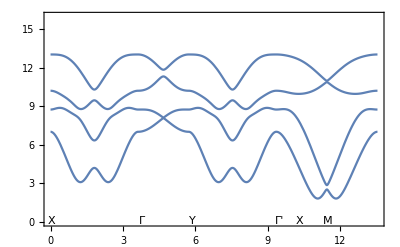

1.

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0;
{phx,phy,phz}=1*hv5;

pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];


For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
MH[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

MMH[qa_,qb_]:=MH[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]
SRM[qa_,qb_]:=MatrixPower[MMH[qa,qb],1/2]
FH[qa_,qb_]:=(1/2)SRM[qa,qb].({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).SRM[qa,qb]
EEM[qa_,qb_]:=Sort[Eigenvalues[FH[qa,qb]]]


Plot[Piecewise[{{EEM[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EEM[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EEM[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EEM[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EEM[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/3+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
(*
Calculate the chern numberp
1.eigenvector of fermion hamiltonian
2. Phases difference of two given vectors,and the order matters.
3. The field strength per plaquette
4. the chern number for given discrete number DN,nthband is the band with nth large eigenvalues *)
nthband=6;
DN=20;
vec[qa_,qb_]:=Module[{eve,eva,p},{eva,eve}=Eigensystem[FH[qa,qb]];
                                     {{p}}=Position[eva,Sort[eva][[nthband]]];
                                      eve[[p]]]
pd[v1_,v2_]:=(Conjugate[v1].v2)/Abs[Conjugate[v1].v2]
fs[qa_,qb_,dk_]:=Re[Log[pd[vec[qa,qb],vec[qa+dk,qb]]*pd[vec[qa+dk,qb],vec[qa+dk,qb+dk]]*pd[vec[qa+dk,qb+dk],vec[qa,qb+dk]]*pd[vec[qa,qb+dk],vec[qa,qb]]]/I]
CN=0;
dk=2*Pi/DN;
For[i=0,i<DN,i++,
For[j=0,j<DN,j++,
CN=CN+fs[2*Pi*i/DN,2*Pi*j/DN,dk];]]
CN/(2Pi)
```

#### Calculate the real space fermion Hamiltonian

```mathematica
NN=200;
FMH[i_,j_]:=1/(NN*NN)Sum[FH[kx,ky]*Exp[-I kx i]*Exp[-I ky j],{kx,0,2Pi-2Pi/NN,2Pi/NN},{ky,0,2Pi-2Pi/NN,2Pi/NN}]
```

```mathematica
FMH[0,0][[2]][[1]]
```

-4.77396×10^-19+7.8019 ⅈ

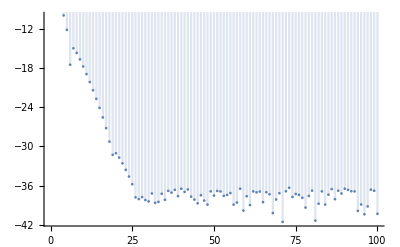

```mathematica
DiscretePlot[Log[Abs[FMH[n,n][[2]][[1]]]],{n,0,100}]
```

```mathematica
MatrixForm[FH[0,0]]
```

(0.+4.75802×10^-16 ⅈ | 0.-9.16808 ⅈ | 0.-7.96932×10^-15 ⅈ | 0.-0.337758 ⅈ | 0.-0.0312905 ⅈ | 0.-1.33439 ⅈ | 0.-0.0503192 ⅈ | 0.-1.59788 ⅈ
0.+9.16808 ⅈ | 0.+1.28196×10^-15 ⅈ | 0.+0.337758 ⅈ | 0.-8.14843×10^-15 ⅈ | 0.+1.37115 ⅈ | 0.-0.0411373 ⅈ | 0.+1.42249 ⅈ | 0.-0.0526657 ⅈ
0.+1.13737×10^-14 ⅈ | 0.-0.337758 ⅈ | 0.-1.61633×10^-15 ⅈ | 0.-9.16808 ⅈ | 0.-0.0503192 ⅈ | 0.-1.59788 ⅈ | 0.-0.0312905 ⅈ | 0.-1.33439 ⅈ
0.+0.337758 ⅈ | 0.+1.10068×10^-14 ⅈ | 0.+9.16808 ⅈ | 0.-1.32576×10^-15 ⅈ | 0.+1.42249 ⅈ | 0.-0.0526657 ⅈ | 0.+1.37115 ⅈ | 0.-0.0411373 ⅈ
0.+0.0312905 ⅈ | 0.-1.37115 ⅈ | 0.+0.0503192 ⅈ | 0.-1.42249 ⅈ | 0.+9.4369×10^-16 ⅈ | 0.-10.3491 ⅈ | 0.+2.8557×10^-14 ⅈ | 0.-0.233812 ⅈ
0.+1.33439 ⅈ | 0.+0.0411373 ⅈ | 0.+1.59788 ⅈ | 0.+0.0526657 ⅈ | 0.+10.3491 ⅈ | 0.+6.66134×10^-16 ⅈ | 0.+0.233812 ⅈ | 0.+3.11973×10^-14 ⅈ
0.+0.0503192 ⅈ | 0.-1.42249 ⅈ | 0.+0.0312905 ⅈ | 0.-1.37115 ⅈ | 0.-3.05311×10^-14 ⅈ | 0.-0.233812 ⅈ | 0.+2.27075×10^-15 ⅈ | 0.-10.3491 ⅈ
0.+1.59788 ⅈ | 0.+0.0526657 ⅈ | 0.+1.33439 ⅈ | 0.+0.0411373 ⅈ | 0.+0.233812 ⅈ | 0.-3.19759×10^-14 ⅈ | 0.+10.3491 ⅈ | 0.+2.18402×10^-15 ⅈ)

```mathematica
Sum[x*y,{x,1,2,0.5},{y,1,2,0.5}]
```

20.25

```mathematica
a={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
b={{a,a},{a,a}}
```

{{{{1,2},{3,4}},{{1,2},{3,4}}},{{{1,2},{3,4}},{{1,2},{3,4}}}}

```mathematica
MatrixForm[ArrayFlatten[b]]
```

(1 | 2 | 1 | 2
3 | 4 | 3 | 4
1 | 2 | 1 | 2
3 | 4 | 3 | 4)